```mathematica
SetDirectory[NotebookDirectory[]];
Get["../source/mathematica/FigureSettings.wl"];
InitializePlotSettings[]
```

```mathematica
dataNum1=Import[FileNameJoin[{NotebookDirectory[],"..","data","pnp_zp1_zn1_Ip2.00_In1.00_eps0.050.csv"}],"CSV"];
{x1,p1,n1,ϕ1}=Transpose[dataNum1[[2;;]]];
```

```mathematica
dataNum2=Import[FileNameJoin[{NotebookDirectory[],"..","data","pnp_zp2_zn1_Ip2.00_In1.00_eps0.050.csv"}],"CSV"];
{x2,p2,n2,ϕ2}=Transpose[dataNum2[[2;;]]];
dataNum3=Import[FileNameJoin[{NotebookDirectory[],"..","data","pnp_zp3_zn1_Ip2.00_In1.00_eps0.050.csv"}],"CSV"];
{x3,p3,n3,ϕ3}=Transpose[dataNum3[[2;;]]];
```

```mathematica
pNum={Transpose[{x1,p1}],Transpose[{x2,p2}],Transpose[{x3,p3}]};
nNum={Transpose[{x1,n1}],Transpose[{x2,n2}],Transpose[{x3,n3}]};
ϕNum={Transpose[{x1,ϕ1}],Transpose[{x2,ϕ2}],Transpose[{x3,ϕ3}]};
```

```mathematica
NumericalPlotP=ListLinePlot[pNum,PlotRange->{{0,1},{0.5,1.6}},PlotRange->{{0,1},{0.6,1.6}},AspectRatio->1,PlotStyle->{Directive[colors[[1]],Thickness[0.008]] ,Directive[colors[[3]],Dashing[{0.04,0.03}],Thickness[0.008]],Directive[colors[[4]],Dashing[{0.01,0.03}],Thickness[0.008]]},ImageSize->Large,FrameStyle->Directive[AbsoluteThickness[2.5]],LabelStyle->Directive[Black]];
NumericalPlotN=ListLinePlot[nNum,PlotRange->{{0,1},{0.8,1.2}},PlotRange->{{0,1},{0.6,1.6}},AspectRatio->1,PlotStyle->{Directive[colors[[1]],Thickness[0.008]] ,Directive[colors[[3]],Dashing[{0.04,0.03}],Thickness[0.008]],Directive[colors[[4]],Dashing[{0.01,0.03}],Thickness[0.008]]},ImageSize->Large,FrameStyle->Directive[AbsoluteThickness[2.5]],LabelStyle->Directive[Black],GridLines->{Automatic,Range[0.8,1.2,0.1]},FrameTicks->{{{{0.8,"0.8"},{0.9,"0.9"},{1.0,"1.0"},{1.1,"1.1"},{1.2,"1.2"}},None},{Automatic,None}}];
NumericalPlotϕ=ListLinePlot[ϕNum,PlotRange->{{0,1},{-0.2,1.2}},PlotRange->{{0,1},{0.6,1.6}},AspectRatio->1,PlotStyle->{Directive[colors[[1]],Thickness[0.008]] ,Directive[colors[[3]],Dashing[{0.04,0.03}],Thickness[0.008]],Directive[colors[[4]],Dashing[{0.01,0.03}],Thickness[0.008]]},ImageSize->Large,FrameStyle->Directive[AbsoluteThickness[2.5]],LabelStyle->Directive[Black],FrameTicks->{{{{0.8,"0.8"},{0.6,"0.6"},{1.0,"1.0"},{0.4,"0.4"},{1.2,"1.2"},{0.2,"0.2"},{0,"0.0"},{-0.2,"-0.2"}},None},{Automatic,None}}];
```

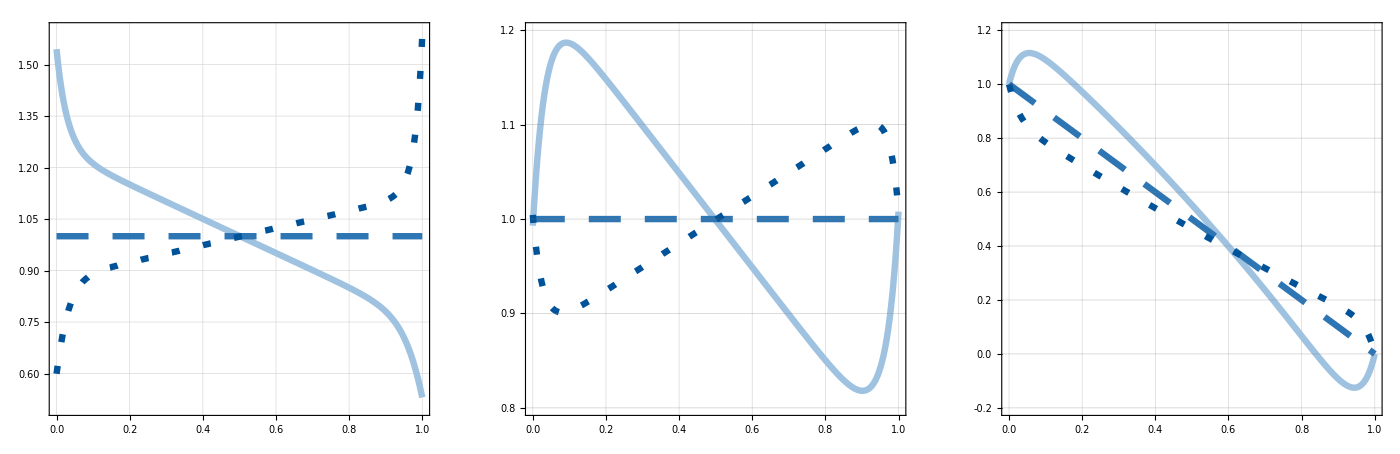

```mathematica
triptychNumerical=GraphicsRow[{NumericalPlotP,NumericalPlotN,NumericalPlotϕ},Spacings->30,ImageSize->1400]
```

Labels and annotations added in photo editing software Canva.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"..","figures","Figure2.pdf"}],triptychNumerical,ImageResolution->300]
```

/Users/georginaryan/Desktop/DPhil/Research/Draft Papers/Journal Article - Chapter 4/Figures Ratio Version/Final Code for Repository/asymmetric-valence-electrolytes/notebooks/../figures/Figure2.pdf